```mathematica
(*srezdata = Cases[data,{_ (*t_ /; (t>=0.03)&&(t<0.04)*),x_ /; x==a  ,_,_}/.a-> 0.40];
tdata = srezdata⟦All, 1⟧;
udata = srezdata⟦All, 3⟧;
listTU ={tdata,udata}^ᵀ;
ListLinePlot[listTU]*)
(*ListContourPlot[data⟦All,1;;3⟧]
ListContourPlot[data⟦All,{1,2,4}⟧]*)
Module[{data},
data =Import["/home/ilya/brusselator/sravn/bruseplb15k.dat", "Table"];
ListPlot3D[data⟦All,1;;3⟧] ;
ListPlot3D[data⟦All,{1,2,4}⟧]
]
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot3D::arrayerr: Symbol[] must be a valid array or a list of valid arrays.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot3D::arrayerr: Symbol[] must be a valid array or a list of valid arrays.

ListPlot3D[Symbol[]]

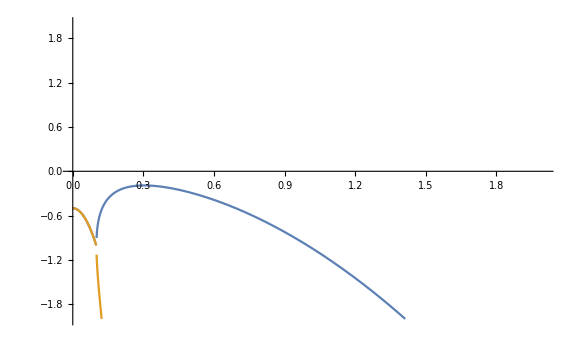

```mathematica
Assuming[{k∈Reals,k>0},
Block[{B=1,A=1,Du=1,Dv=100},
p1[k_] := 0.5*(B-1-A^2-(Du+Dv)k^2+Sqrt[(B-1-A^2-(Du+Dv)k^2)^2-4 A^2 B+4 (B-1-k^2 Du)(A^2+k^2 Dv)]);
p2[k_] := 0.5*(B-1-A^2-(Du+Dv)k^2-Sqrt[(B-1-A^2-(Du+Dv)k^2)^2-4 A^2 B+4 (B-1-k^2 Du)(A^2+k^2 Dv)]);
realp1[k_] :=Re@p1[k];
realp2[k_] :=Re@p2[k];
(*Export["/home/ilya/brusselator/plots/dispersB=1.png",Show[Plot[{ realp1[k],realp2[k]},{k,0,2}, PlotRange->{{0,2}, {-2,2}}, ImageSize->Large]]]; *)
Show[Plot[{ realp1[k],realp2[k]},{k,0,2}, PlotRange->{{0,2}, {-2,2}}, ImageSize->Large]]
]
]
```